```mathematica
data = Import[NotebookDirectory[] <> "../data/btc future and reference rate/coingecko_future.csv"];
```

```mathematica
data[[1;;3]]
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
0 | 2021-02-03 | 37266.4 | 37790. | 0.0452987 | 0.0337738
1 | 2021-02-02 | 35615.9 | 36535. | 0.059664 | 0.0641463)

```mathematica
dates=Table[DateObject[data⟦k,2⟧],{k,2,Length[data]}];
```

```mathematica
Length[dates]
```

678

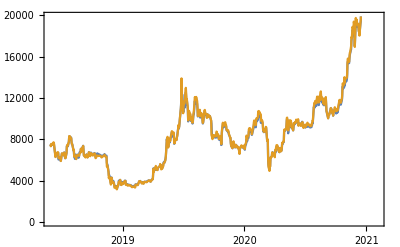

```mathematica
DateListPlot[{{dates,data[[2;;,3]]}ᵀ, {dates, data[[2;;,4]]}ᵀ}]
```

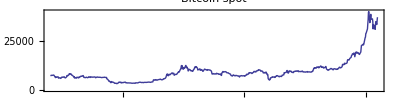

```mathematica
p1=DateListPlot[{dates,data[[2;;,3]]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Bitcoin spot",AspectRatio->1/4,PlotRange->Full]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_level_series.pdf", p1]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_level_series.pdf

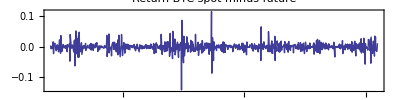

```mathematica
p1a=DateListPlot[{dates,Exp[data⟦2;;All,5⟧]-Exp[data⟦2;;All,6⟧]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Return BTC spot minus future",AspectRatio->1/4,PlotRange->Full]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_vs_future_series.pdf", p1a]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_vs_future_series.pdf

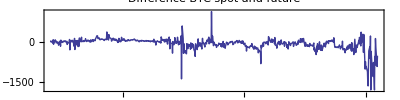

```mathematica
p2=DateListPlot[{dates,data[[2;;,3]]-data[[2;;,4]]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Difference BTC spot and future",PlotRange->All,AspectRatio->1/4]
```

```mathematica
(*Export[NotebookDirectory[] <> "../latex/_pics/btc_vs_future_series.pdf", p2]*)
```

```mathematica
(*p2=DateListPlot[{dates,data[[2;;,3]]-data[[2;;,4]]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Difference BTC spot and future",PlotRange->All,AspectRatio->1/4]*)
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_vs_future_series.pdf

```mathematica
r=data⟦2;;All,5⟧;
f=data⟦2;;All,6⟧;
sr=Sort[r];
m=Mean[r];
s=StandardDeviation[r];
l=Length[r];
```

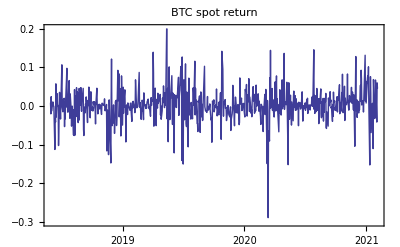

```mathematica
p3=DateListPlot[{dates,r}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"BTC spot return",PlotRange->{-0.3, 0.2}]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_return_series.pdf", p3]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_return_series.pdf

```mathematica
extremes=Sort[Abs[r]]⟦-30;;All⟧;
pos=Flatten[Table[Position[Abs[r],extremes⟦k⟧],{k,1,Length[extremes]}]];
```

```mathematica
p3a=DateListPlot[Transpose[{dates⟦pos⟧,r⟦pos⟧}],PlotStyle->{Red,Thick},Joined->False];
```

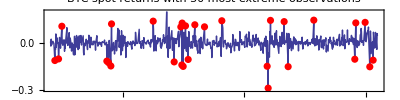

```mathematica
p3b=Show[p3,p3a, PlotLabel->"BTC spot returns with 30 most extreme observations",AspectRatio->1/4]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_series.pdf", p3b]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_series.pdf

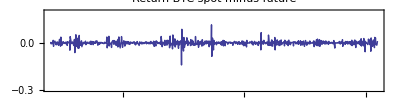

```mathematica
p1a=DateListPlot[{dates,Exp[data⟦2;;All,5⟧]-Exp[data⟦2;;All,6⟧]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Return BTC spot minus future",AspectRatio->1/4,PlotRange->{-0.3, 0.2}]
```

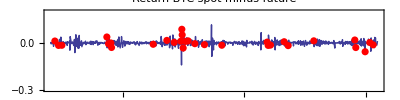

```mathematica
p1c=Show[p1a,DateListPlot[Transpose[{dates⟦pos⟧,(Exp[data⟦2;;All,5⟧]-Exp[data⟦2;;All,6⟧])⟦pos⟧}],PlotStyle->{Red,Thick},Joined->False]]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_vs_future_series.pdf", p1c]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_vs_future_series.pdf

```mathematica
NMaximize[{LogLikelihood[StudentTDistribution[ν], (r-m)/s],ν>2}, ν]
```

{-930.714,{ν→7.94508}}

Generalized Pareto distribution

```mathematica
K=Ceiling[l 0.05];
u=-sr⟦K⟧
```

0.0652943

```mathematica
y=-sr⟦1;;K-1⟧-u;
```

```mathematica
g[x_,β_,ξ_]:=1-(1+ξ x/β)^(-1/ξ)
```

```mathematica
NMaximize[{Total[Log[g[y,β,ξ]]],ξ>0&& β>0},{β,ξ}]
```

{0.,{β→6.58869×10^-8,ξ→0.203272}}

```mathematica
1/0.203272
```

4.91952

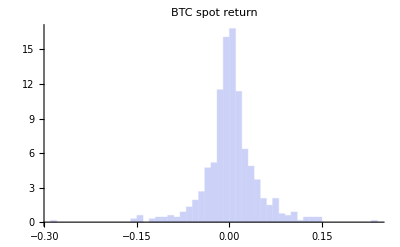

```mathematica
p4=Histogram[data[[2;;,5]],Automatic, "PDF", PlotTheme->"Classic", PlotLabel->"BTC spot return",PlotRange->All]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_hist.pdf", p4]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_hist.pdf

See gretl for summary statistics

```mathematica
t=Table[{InverseCDF[NormalDistribution[m,s],(k-0.5)/l],sr[[k]]}, {k,1,l}];
```

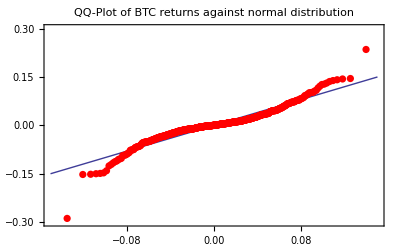

```mathematica
p5=Show[
Plot[x, {x,-0.15, 0.15},PlotTheme->"Classic",PlotRange->{-0.3,0.3}, Frame->True,PlotLabel->"QQ-Plot of BTC returns against normal distribution"],
ListPlot[t, PlotTheme->"Classic", PlotStyle->{Red, PointSize[0.013]},PlotRange->All]
]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_qq.pdf", p5]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_qq.pdf

Outliers are 3/2 times beyond the interquartile range; far outliers are beyond 3 times  the interquartile range.

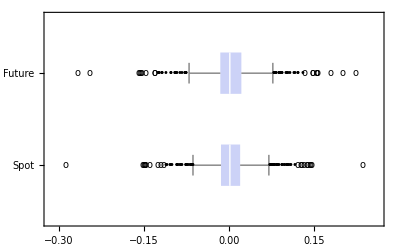

```mathematica
p6=BoxWhiskerChart[{r,f},{{"Outliers", "•"},{"FarOutliers", o}},PlotTheme->"Classic",  ChartLabels->{"Spot", "Future"},BarOrigin->Left]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_future_box.pdf", p6]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_future_box.pdf

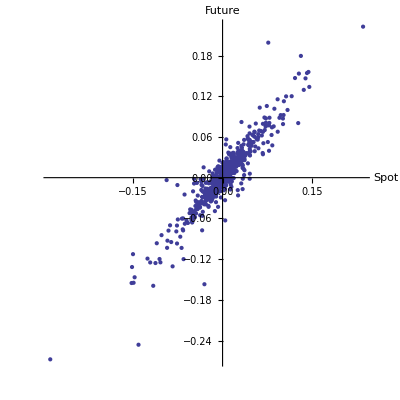

```mathematica
p7=ListPlot[{r,f}ᵀ,PlotTheme->"Classic",AxesLabel->{"Spot", "Future"},PlotRange->All, AspectRatio->1]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_future_scatter.pdf", p7]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_future_scatter.pdf

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
usim=hatF[r];
vsim=hatF[f];
```

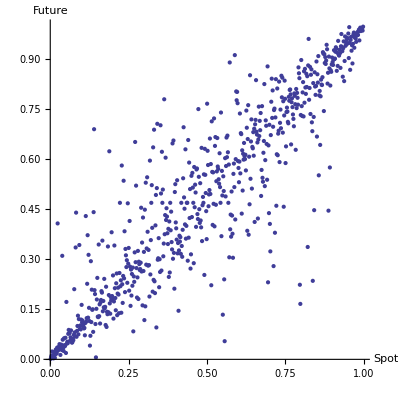

```mathematica
p8=ListPlot[{usim,vsim}ᵀ,PlotTheme->"Classic",AxesLabel->{"Spot", "Future"},PlotRange->All, AspectRatio->1]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_future_copula_scatter.pdf", p8]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_future_copula_scatter.pdf

## Copula scatterplots

```mathematica
Clear[u,v,ρ,p]
```

```mathematica
sp[dist_]:=12 NIntegrate[CDF[dist,{u,v}], {u,0,1}, {v,0,1}]-3
```

Gaussian copula / Spearman’s rho

```mathematica
sol=Solve[ 6/Pi ArcSin[1/2 ρ]==0.75,ρ]
```

{{ρ→0.765367}}

```mathematica
gaussian = CopulaDistribution[{"Binormal", ρ/.sol[[1]]}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[gaussian]
```

0.75

```mathematica
Plot3D[PDF[gaussian, {u,v}], {u,0,1}, {v,0,1},PlotTheme->"Classic"]
```

-Graphics3D-

```mathematica
r1=RandomVariate[gaussian, 1000];
```

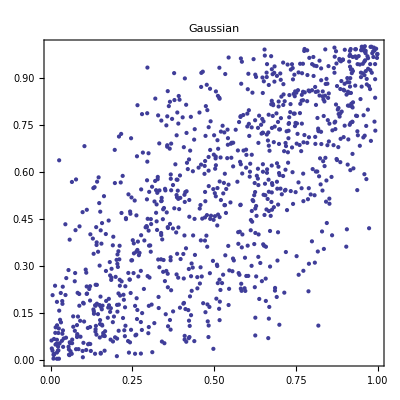

```mathematica
p1=ListPlot[r1,PlotTheme->"Classic", PlotStyle->Thick,Frame->True,PlotLabel->"Gaussian", AspectRatio->1]
```

Multivariate T

```mathematica
ρ=0.77025;StudentT=CopulaDistribution[{"MultivariateT", {{1,ρ}, {ρ,1}}, 10}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[StudentT]
```

0.749847

```mathematica
r2=RandomVariate[StudentT, 1000];
```

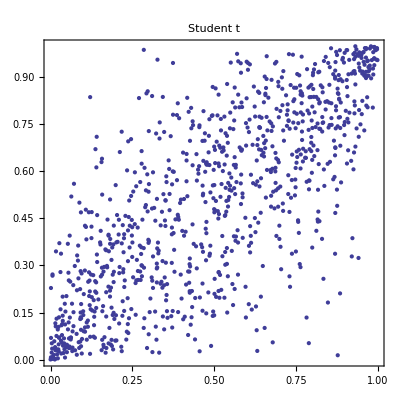

```mathematica
p2=ListPlot[r2,PlotTheme->"Classic", PlotStyle->Thick,Frame->True,PlotLabel->"Student t", AspectRatio->1]
```

Clayton

```mathematica
c=0.3875;
clayton = CopulaDistribution[{"Clayton", c}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[clayton]
```

0.75009

```mathematica
r3=RandomVariate[clayton, 1000];
```

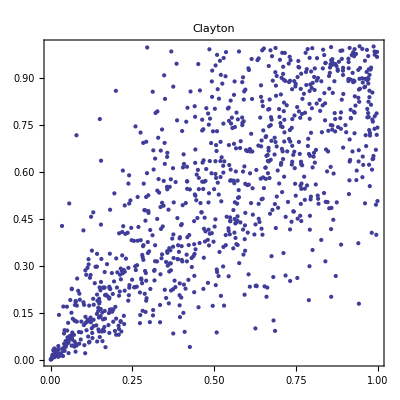

```mathematica
p3=ListPlot[r3,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Clayton", AspectRatio->1]
```

Frank

```mathematica
α=0.001199;
frank = CopulaDistribution[{"Frank", α}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[frank]
```

0.750022

```mathematica
r4=RandomVariate[frank, 1000];
```

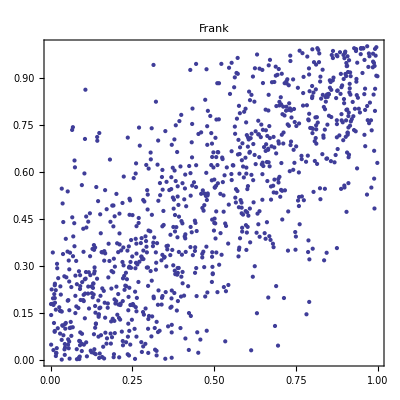

```mathematica
p4=ListPlot[r4,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Frank", AspectRatio->1]
```

Gumbel

```mathematica
α=2.2855;
gumbel=CopulaDistribution[{"GumbelHougaard", α}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[gumbel]
```

0.750056

```mathematica
r5=RandomVariate[gumbel, 1000];
```

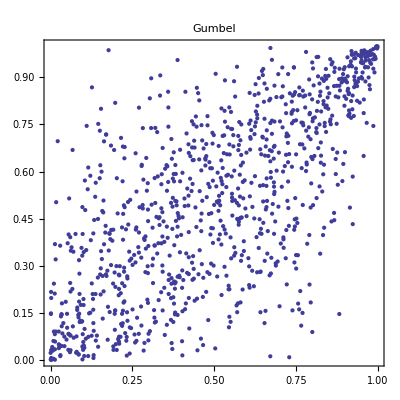

```mathematica
p5=ListPlot[r5,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Gumbel", AspectRatio->1]
```

Plackett
From Nelsen, p.99/100

From Nelsen, p. 171:

```mathematica
Clear[θ]
NSolve[0.75==(θ+1)/(θ-1)-(2 θ Log[θ])/(θ-1)^2,θ]
```

NSolve[0.75==(θ+1)/(θ-1)-(2 θ log(θ))/(θ-1)^2,θ]

```mathematica
sol=NMinimize[{(0.75-((θ+1)/(θ-1)-(2 θ Log[θ])/(θ-1)^2))^2,θ>0},{θ,15,20}]
```

{6.48932×10^-16,{θ→17.1395}}

```mathematica
θ=θ/.sol[[2]];
u=RandomVariate[UniformDistribution[],1000];
t=RandomVariate[UniformDistribution[],1000];
```

```mathematica
a=t (1-t);
b=θ+a (θ-1)^2;
c=2 a (u θ^2+1-u)+θ (1-2 a);
d=√θ √(θ+4 a u (1-u) (1-θ)^2);
v=(c-(1-2t )d)/(2 b);
```

```mathematica
r6 = {u,v}ᵀ;
```

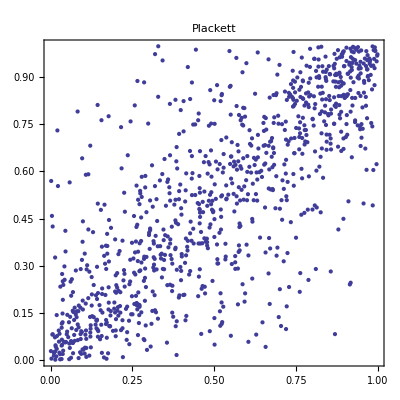

```mathematica
p6=ListPlot[r6,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Plackett", AspectRatio->1]
```

NIG factor model

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

```mathematica
α=1.5;
β=0.1;
Clear[δ]
```

Spearman Rho approximation of Gaussian

```mathematica
sol=NSolve[(6 ArcSin[δ/(2 δs[α,β])])/π==0.75, δ]
```

{{δ→1.14041}}

```mathematica
δ=δ/.sol⟦1⟧;
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
```

```mathematica
Y=RandomVariate[NormalDistribution[],{3,1000}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], 1000];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], 1000];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], 1000];
```

```mathematica
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
```

```mathematica
SpearmanRho[X1,X2]
```

0.727213

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Timing[
usim = hatF[X1];
vsim = hatF[X2];
]
```

{0.042076,Null}

```mathematica
r7 = {usim,vsim}ᵀ;
```

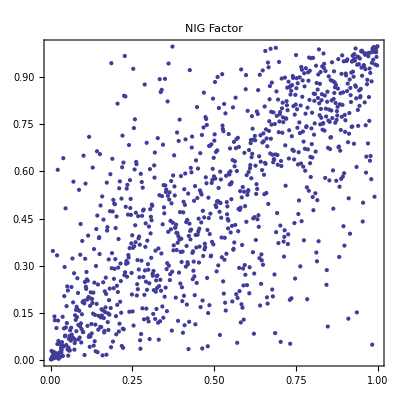

```mathematica
p7=ListPlot[r7,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"NIG Factor", AspectRatio->1]
```

Mixture copula

```mathematica
Clear[ρ,p]
```

```mathematica
p=0.8;
sol=Solve[ p 6/Pi ArcSin[1/2 ρ]==0.75,ρ]
```

{{ρ→0.942793}}

```mathematica
ρ=ρ/.sol[[1]]
```

0.942793

```mathematica
mixture = p CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}] + (1-p) CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}]]
```

-8.88178×10^-16

```mathematica
p sp[CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}]]
```

0.75

```mathematica
Plot3D[p PDF[CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}],{u,v}]+ (1-p) PDF[CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}],{u,v}], {u,0,1}, {v,0,1}]
```

-Graphics3D-

```mathematica
X=RandomVariate[NormalDistribution[],1000];
Z=RandomVariate[NormalDistribution[],1000];
W=RandomVariate[UniformDistribution[],1000];
```

```mathematica
Y=ConstantArray[0, 1000];
```

```mathematica
Table[If[W⟦k⟧≤p,Y⟦k⟧=ρ X⟦k⟧+√(1-ρ^2) Z⟦k⟧,Y⟦k⟧=Z⟦k⟧],{k,1,1000}];
```

```mathematica
Timing[
usim = hatF[X];
vsim = hatF[Y];
]
```

{0.041612,Null}

```mathematica
r8 = {usim,vsim}ᵀ;
```

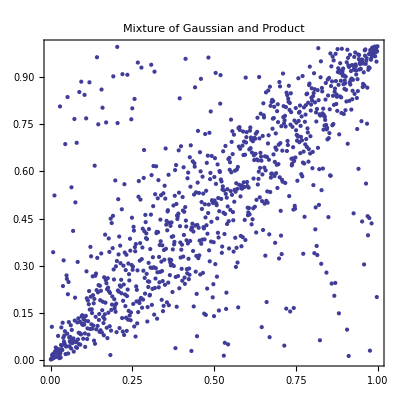

```mathematica
p8=ListPlot[r8,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Mixture of Gaussian and Product", AspectRatio->1]
```

```mathematica
(*p CDF[CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}],{u,v}]+ (1-p)CDF[CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}],{u,v}]/.{u->.85, v->.65}*)
```

```mathematica
Length[Select[{usim, vsim}ᵀ, #1[[1]]<=0.85 && #1[[2]]≤0.65&]]/1000.
```

0.631

```mathematica
Grid[{{p1, p2, p3, p4}, {},{p5, p6, p7, p8}}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/copulas_scatterplots.pdf", %]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/copulas_scatterplots.pdf

## h Parameters

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
hParams=Import[NotebookDirectory[] <> "../results/coingecko_future_v3/MM/OHR.csv"];
```

```mathematica
Dimensions[hParams]
```

{3601,5}

```mathematica
dates={};
For[k=0, k≤74, k++,
d=Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/"<> ToString[k] <> ".csv"];
AppendTo[dates,DateObject[d⟦2,2⟧]];
]
```

```mathematica
hParams[[1;;10]]
```

( | file_name | risk_measure | OHR | copula
0 | 73.csv | ERM k=10 | 0.920996 | Gaussian
1 | 73.csv | ES q=0.01 | 0.845898 | Gaussian
2 | 73.csv | ES q=0.05 | 0.914258 | Gaussian
3 | 73.csv | VaR q=0.01 | 0.928906 | Gaussian
4 | 73.csv | VaR q=0.05 | 0.957031 | Gaussian
5 | 73.csv | Variance | 0.907715 | Gaussian
6 | 36.csv | ERM k=10 | 0.872266 | Gaussian
7 | 36.csv | ES q=0.01 | 0.921973 | Gaussian
8 | 36.csv | ES q=0.05 | 0.88877 | Gaussian)

```mathematica
copulas=Union[hParams[[2;;,5]], {}];
measures=Union[hParams[[2;;,3]], {}];
```

```mathematica
copulas
```

{Clayton,Frank,Gaussian,Gauss Mix Indep,Gumbel,Plackett,t_Copula,t_Copula_Capped}

```mathematica
measures
```

{ERM k=10,ES q=0.01,ES q=0.05,Variance,VaR q=0.01,VaR q=0.05}

```mathematica
methods
```

{Variance,VaR 99%,VaR 95%,ES 99%,ES 95%,Spectral 10}

```mathematica
measures={measures⟦4⟧,measures⟦5⟧,measures⟦6⟧,measures⟦2⟧,measures⟦3⟧,measures⟦1⟧}
```

{Variance,VaR q=0.01,VaR q=0.05,ES q=0.01,ES q=0.05,ERM k=10}

```mathematica
hGaussian=Select[hParams, #1[[5]]=="Gaussian"&];
```

```mathematica
hGaussian[[1;;10]]
```

(0 | 73.csv | ERM k=10 | 0.920996 | Gaussian
1 | 73.csv | ES q=0.01 | 0.845898 | Gaussian
2 | 73.csv | ES q=0.05 | 0.914258 | Gaussian
3 | 73.csv | VaR q=0.01 | 0.928906 | Gaussian
4 | 73.csv | VaR q=0.05 | 0.957031 | Gaussian
5 | 73.csv | Variance | 0.907715 | Gaussian
6 | 36.csv | ERM k=10 | 0.872266 | Gaussian
7 | 36.csv | ES q=0.01 | 0.921973 | Gaussian
8 | 36.csv | ES q=0.05 | 0.88877 | Gaussian
9 | 36.csv | VaR q=0.01 | 0.85791 | Gaussian)

```mathematica
p={};
hFull={};
For[j=1, j≤Length[copulas], j++,
h={};
For[k=1, k≤Length[measures], k++,
htmp1=Select[hParams,#1⟦5⟧==copulas⟦j⟧&];
htmp=Select[htmp1,#1⟦3⟧==measures⟦k⟧&];
o=Ordering[ToExpression[StringReplace[htmp⟦1;;All,2⟧,".csv"->""]]];
AppendTo[h,htmp⟦o,4⟧];
];
AppendTo[p,DateListPlot[Table[{dates,h⟦k⟧}ᵀ,{k,1,Length[h]}],(*PlotLegends->measures,*)PlotLabel->copulas⟦j⟧,PlotRange->{0,1.2}]];
AppendTo[hFull, h];
]
```

Add NIG factor

```mathematica
hvec={};
For[j=0, j≤74, j++,
AppendTo[hvec, Import[NotebookDirectory[] <> "data/" <> ToString[j] <> "_h.csv"]];
(* order of risk measures: variance, VaR99, VaR95, ES99, ES95, Spectral10 *)
]
```

```mathematica
AppendTo[copulas, "NIG Factor"];
```

```mathematica
h={};
AppendTo[h,hvec[[;;,2]]];
AppendTo[h,hvec[[;;,3]]];
AppendTo[h,hvec[[;;,4]]];
AppendTo[h,hvec[[;;,5]]];
AppendTo[h,hvec[[;;,6]]];
AppendTo[h,hvec[[;;,7]]];
```

```mathematica
AppendTo[hFull,h[[;;,;;,1]]];
```

```mathematica
AppendTo[p,DateListPlot[Table[Transpose[{dates,h⟦k⟧}],{k,1,Length[h]}],(*PlotLegends->measures,*)PlotLabel->"NIG Factor",PlotRange->{0,1.2}]];
```

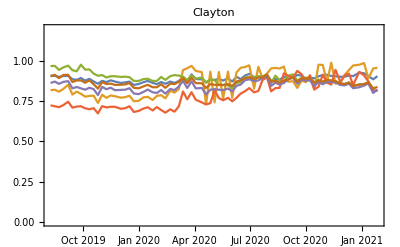
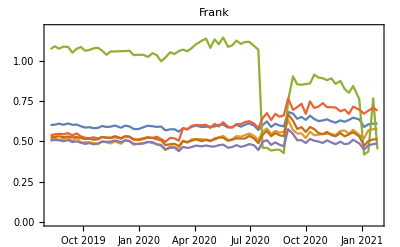
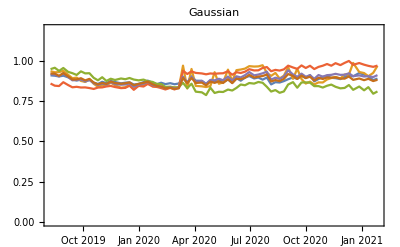
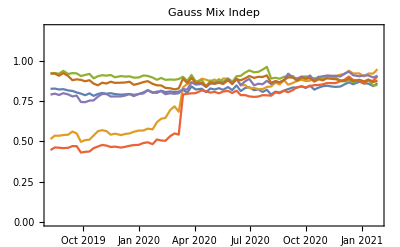
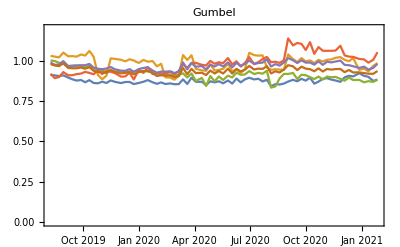
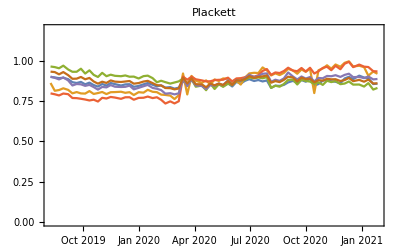
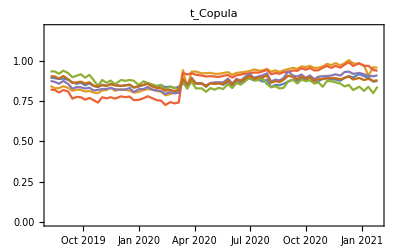
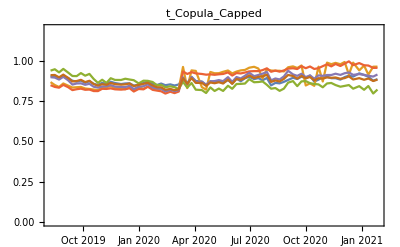

```mathematica
p
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/hParams_Legend.pdf",LineLegend[ColorData[97, "ColorList"],methods, LegendLayout->"Row"]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/hParams_Legend.pdf

```mathematica
Export[NotebookDirectory[]<> "../latex/_pics/hParams.pdf", Grid[{{p⟦3⟧,p⟦7⟧,p⟦1⟧,p⟦2⟧},{p⟦5⟧,p⟦6⟧,p⟦9⟧,p⟦4⟧}}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/hParams.pdf

## P&L

```mathematica
Dimensions[hFull]
```

{9,6,75}

```mathematica
Dimensions[hFull⟦1⟧]
```

{6,75}

h’s were generated with 30 days test in mind. For 100 days test, we need to discard data until 10 Sep 2020. 
Starting index:

```mathematica
dates⟦20⟧
```

Thu 10 Sep 2020

```mathematica
htmp=hFull[[9]];
```

```mathematica
htmp[[;;,20]]
```

{0.850481,0.888836,0.877198,0.875857,0.878191,0.848304}

### In-sample P&L

```mathematica
methods
measures
copulas
```

{Variance,VaR 99%,VaR 95%,ES 99%,ES 95%,Spectral 10}

{Variance,VaR q=0.01,VaR q=0.05,ES q=0.01,ES q=0.05,ERM k=10}

{Clayton,Frank,Gaussian,Gauss Mix Indep,Gumbel,Plackett,t_Copula,t_Copula_Capped,NIG Factor}

```mathematica
For[ii=1, ii≤ Length[copulas], ii++,
htmp=hFull[[ii]];
For[kk=0, kk≤54, kk++,
data = (* in sample *)
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[20+kk] <> ".csv"];
dates=Table[DateList[{data⟦k,2⟧,{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,6⟧];
brr=Reverse[data⟦2;;All,5⟧];
(* hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"]; *)
hvec=htmp[[;;,20+kk]];
PLdyn={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLstat={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PLdyn, PLbrr];
AppendTo[PLstat,Flatten[{"unhedged",Exp[Accumulate[rbrr]]}]];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PLdyn,PLbtc];
AppendTo[PLstat,Flatten[{"future", Exp[Accumulate[rbtc]]}]];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=1, jj≤Length[hvec],jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0; (* dynamic hedge; every day starts with h units of future *)
rh=Log[(1+PLh)];
PLs=Exp[Accumulate[rh]];
PrependTo[PLh, methods⟦jj⟧];
AppendTo[PLdyn, PLh];
PrependTo[PLs, methods⟦jj⟧];
AppendTo[PLstat, PLs];
PrependTo[rh, methods⟦jj⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_"<> copulas[[ii]] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_"<>copulas[[ii]]<> "_PLr_insample.csv",PLrᵀ]
]
]
```

### Out-of-sample P&L

We use the h’s calibrated every 5 days on 300 days of history and build out-of-sample data sets of size 100

```mathematica
For[ii=1, ii≤  Length[copulas], ii++,
htmp=hFull⟦ii⟧;
For[kk=0, kk≤ 54, kk++,
data = (* out-of-sample *)
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v5/test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{data⟦k,2⟧,{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,6⟧];
brr=Reverse[data⟦2;;All,5⟧];
(*  hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];*)
hvec=htmp[[;;,20+kk]];
PLdyn={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};PLstat={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PLdyn, PLbrr];
AppendTo[PLstat,Flatten[{"unhedged",Exp[Accumulate[rbrr]]}]];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PLdyn,PLbtc];
AppendTo[PLstat,Flatten[{"future", Exp[Accumulate[rbtc]]}]];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=1, jj≤Length[hvec],jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PLs=Exp[Accumulate[rh]];
PrependTo[PLh, methods⟦jj⟧];
AppendTo[PLdyn, PLh];
PrependTo[PLs, methods⟦jj⟧];
AppendTo[PLstat, PLs];
PrependTo[rh, methods⟦jj⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_"<> copulas[[ii]] <> "_PL_outsample.csv",PLdynᵀ];
Export[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_"<>copulas[[ii]]<> "_PLr_outsample.csv",PLrᵀ]
]
]
```

### Out-of-sample P&L (5 days)

We use the h’s calibrated every 5 days on 300 days of history and build out-of-sample data sets of size 5

```mathematica
For[ii=1, ii≤ Length[copulas], ii++,
htmp=hFull⟦ii⟧;
For[kk=0, kk≤ 74, kk++,
data = (* out-of-sample *)
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{data⟦k,2⟧,{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,6⟧];
brr=Reverse[data⟦2;;All,5⟧];
(*  hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];*)
hvec=htmp⟦1;;All,1+kk⟧;
PLdyn={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};PLstat={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PLdyn, PLbrr];
AppendTo[PLstat,Flatten[{"unhedged",Exp[Accumulate[rbrr]]}]];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PLdyn,PLbtc];
AppendTo[PLstat,Flatten[{"future", Exp[Accumulate[rbtc]]}]];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=1, jj≤Length[hvec],jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PLs=Exp[Accumulate[rh]];
PrependTo[PLh, methods⟦jj⟧];
AppendTo[PLdyn, PLh];
PrependTo[PLs, methods⟦jj⟧];
AppendTo[PLstat, PLs];
PrependTo[rh, methods⟦jj⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data_PL_5Days/" <> ToString[kk] <> "_"<> copulas[[ii]] <> "_PL_outsample.csv",PLdynᵀ];
Export[NotebookDirectory[] <> "data_PL_5Days/" <> ToString[kk] <> "_"<>copulas[[ii]]<> "_PLr_outsample.csv",PLrᵀ]
]
]
```

## P&L Plots

Which kind of P&L to look at? 
- 5 days (this would be daily return P&L, recalibrated as often as possible)
- 100 days (this would be the P&L of a static hedge, so only final P&L counts)

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

#### Out-of-sample (static)

This uses a out-of-sample period of 100 days.

```mathematica
dFull={};
For[ii=1, ii≤Length[copulas],ii++,
d={};
For[kk=0, kk≤54, kk++,
d1=Import[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_" <> copulas[[ii]]<> "_PLr_outsample.csv"];
If[kk==0,
d=Append[{d1[[1,2;;]]}, Exp[Total[d1[[2;;,2;;]]]]],
d=AppendTo[d,Exp[Total[d1[[2;;,2;;]]]]]
];
];
AppendTo[dFull, d];
]
```

```mathematica
Dimensions[dFull]
```

{9,56,8}

```mathematica
dFull[[1,1;;10]]//TableForm
```

unhedged | future | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
3.60305 | 3.6636 | 1.10865 | 1.14675 | 1.07991 | 1.11436 | 1.11173 | 1.10804
2.72914 | 2.78403 | 1.06267 | 1.10571 | 1.06005 | 1.06088 | 1.08748 | 1.08748
3.04684 | 3.08469 | 1.08804 | 1.00289 | 1.1212 | 1.05663 | 1.13844 | 1.11998
2.9733 | 2.99029 | 1.11959 | 1.02974 | 1.12392 | 1.18918 | 1.16162 | 1.14457
2.93876 | 3.00552 | 1.09291 | 1.00545 | 1.06505 | 1.16787 | 1.12128 | 1.10637
2.27349 | 2.32649 | 1.0709 | 0.995637 | 1.08501 | 1.13679 | 1.10276 | 1.07676
2.02446 | 1.98265 | 1.07242 | 1.06863 | 1.07289 | 1.08653 | 1.08009 | 1.07202
1.93953 | 1.89087 | 1.09151 | 1.09532 | 1.08412 | 1.10133 | 1.09173 | 1.08874
2.04651 | 2.05487 | 1.06223 | 1.01267 | 1.06133 | 1.13908 | 1.08283 | 1.06819

```mathematica
p={};
For[ii=1, ii<=Length[copulas], ii++,
AppendTo[p, BoxWhiskerChart[dFull[[ii,2;;]]ᵀ, ChartLabels->dFull[[ii,1]],PlotRange->{Automatic,Full},PlotTheme->"Classic", PlotLabel->copulas[[ii]]]];
]
```

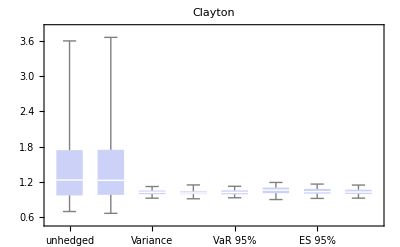
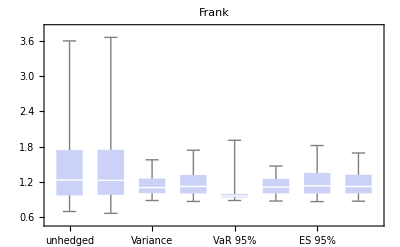
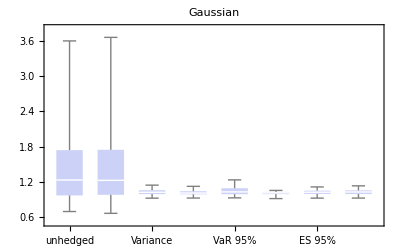
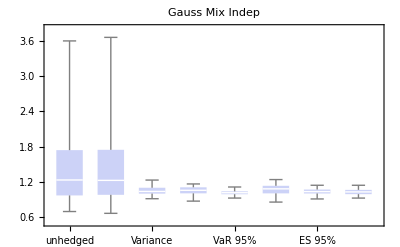
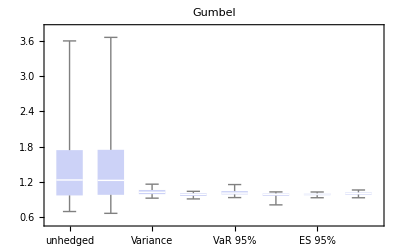
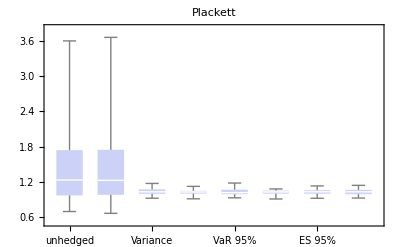
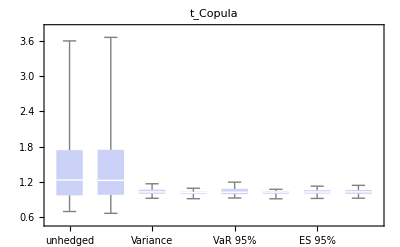
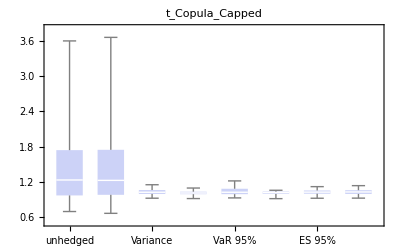

```mathematica
p
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/PL_static_out_tcop.pdf",p[[7]]];
```

```mathematica
p={};
For[ii=1, ii<=Length[copulas], ii++,
AppendTo[p,  BoxWhiskerChart[dFull⟦ii,2;;All,3;;All⟧ᵀ, (*ChartLabels->dFull[[ii,1,3;;]],*)PlotRange->{Automatic,{0.8,2}},PlotTheme->"Classic", PlotLabel->copulas⟦ii⟧]];
]
```

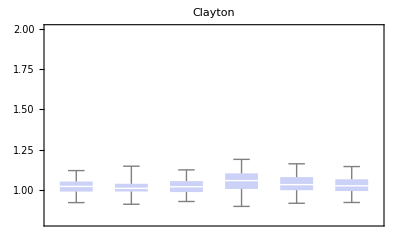
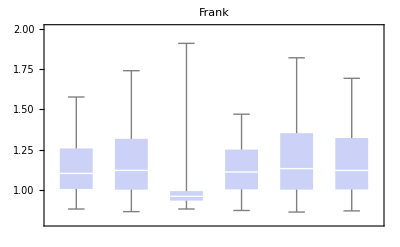
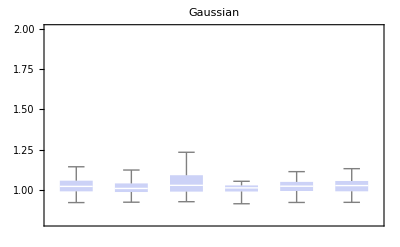
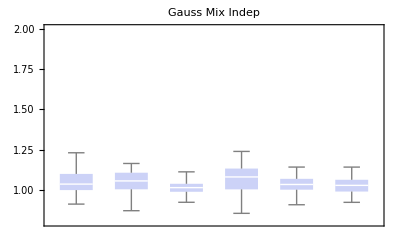
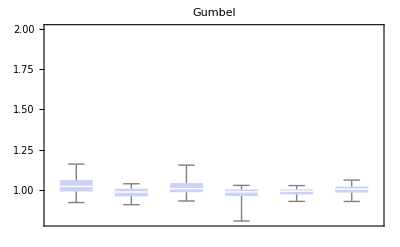
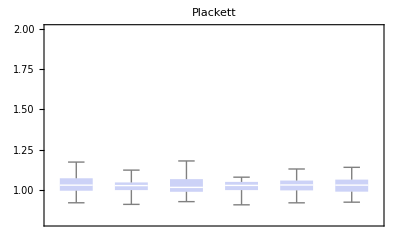
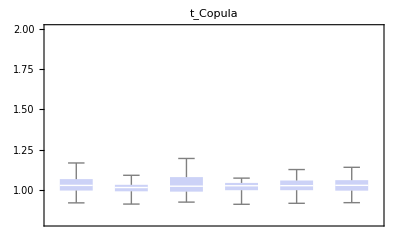
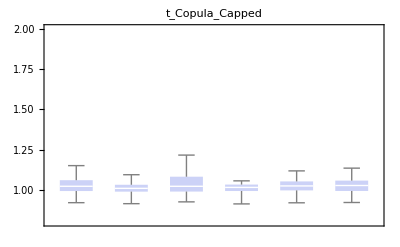

```mathematica
p
```

```mathematica
Export[NotebookDirectory[]<> "../latex/_pics/PL_static_out.pdf", Grid[{{p⟦3⟧,p⟦7⟧,p⟦1⟧,p⟦2⟧},{p⟦5⟧,p⟦6⟧,p⟦9⟧,p⟦4⟧}}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/PL_static_out.pdf

#### Out-of-sample (dynamic)

Uses 5 days of out-of-sample data

```mathematica
dFull={};
For[ii=1, ii≤Length[copulas],ii++,
d={};
For[kk=0, kk≤74, kk++,
d1=Import[NotebookDirectory[] <> "data_PL_5Days/" <> ToString[kk] <> "_" <> copulas[[ii]]<> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d, d1],
d=Join[d,d1[[2;;]]]
];
];
AppendTo[dFull, d];
]
```

```mathematica
Dimensions[dFull]
```

{9,376,9}

```mathematica
dFull[[1,-10;;]]//TableForm
```

2019-08-22 | 0.00965171 | 0.0369081 | -0.0246839 | -0.0213851 | -0.0270879 | -0.017458 | -0.02333 | -0.0249587
2019-08-21 | 0.026051 | 0.0191103 | 0.00886485 | 0.0105032 | 0.00767263 | 0.0124572 | 0.00953694 | 0.00872851
2019-08-20 | 0.00820421 | 0.00138408 | 0.00695823 | 0.00707616 | 0.00687253 | 0.00721703 | 0.00700658 | 0.00694842
2019-08-19 | -0.0680696 | -0.0603365 | -0.0128118 | -0.0179099 | -0.00912348 | -0.0240352 | -0.014899 | -0.0123891
2019-08-16 | 0.00210591 | 0.00634613 | -0.0036693 | -0.00312159 | -0.00406749 | -0.00246759 | -0.00344469 | -0.00371486
2019-08-15 | 0.0153562 | 0.0221627 | -0.0048902 | -0.00286458 | -0.00622822 | -0.000759814 | -0.00386809 | -0.00478465
2019-08-14 | -0.0450054 | -0.0336449 | -0.0140579 | -0.0170836 | -0.0120677 | -0.0202438 | -0.0155827 | -0.0142152
2019-08-13 | -0.0444052 | -0.05269 | 0.00317558 | -0.00144175 | 0.00620879 | -0.00627214 | 0.000849552 | 0.00293573
2019-08-12 | -0.0660253 | -0.077791 | 0.00407078 | -0.00266319 | 0.00848672 | -0.00972322 | 0.000680251 | 0.00372132
2019-08-09 | 0.0131289 | -0.00195122 | 0.0148747 | 0.0147017 | 0.0149887 | 0.0145216 | 0.0147875 | 0.0148657

```mathematica
p={};
For[ii=1, ii<=Length[copulas], ii++,
AppendTo[p, BoxWhiskerChart[dFull[[ii,2;;,2;;]]ᵀ, ChartLabels->dFull[[ii,1,2;;]],PlotRange->{Automatic,Full},PlotTheme->"Classic", PlotLabel->copulas[[ii]]]];
]
```

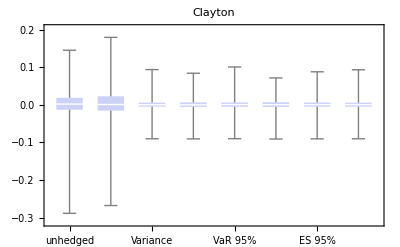
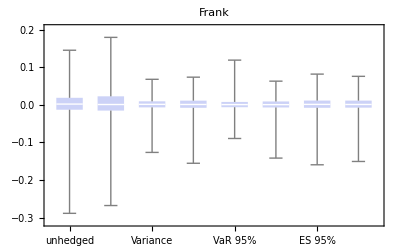
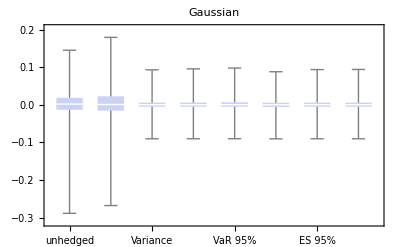
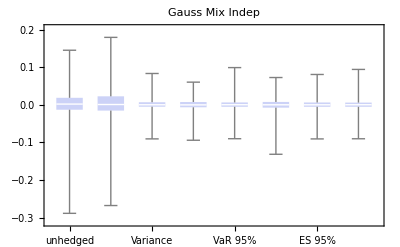
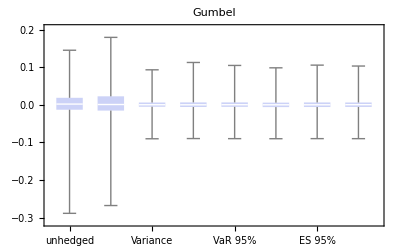
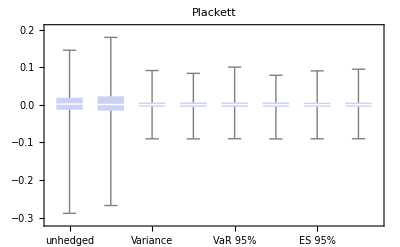
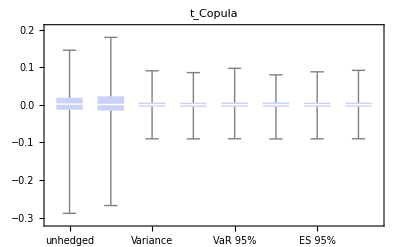
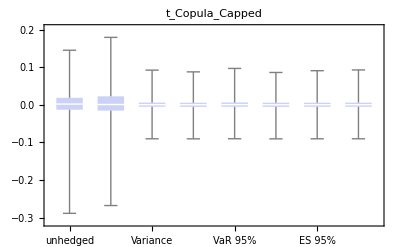

```mathematica
p
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/PL_dynamic_out_tcop.pdf",p[[7]]];
```

```mathematica
p[[7]]
```

-Graphics-

```mathematica
p={};
For[ii=1, ii<=Length[copulas], ii++,
AppendTo[p,  BoxWhiskerChart[dFull⟦ii,2;;All,4;;All⟧ᵀ, (*ChartLabels->dFull[[ii,1,3;;]],*)PlotRange->{Automatic,{-0.15,0.15}},PlotTheme->"Classic", PlotLabel->copulas⟦ii⟧]];
]
```

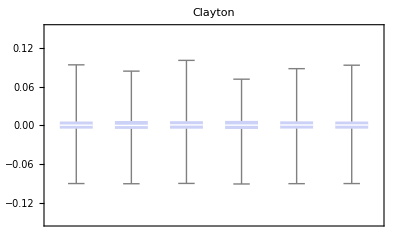
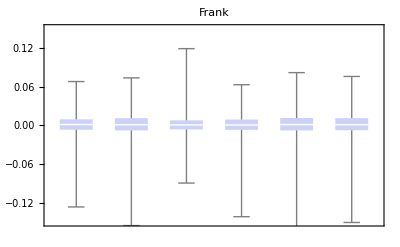
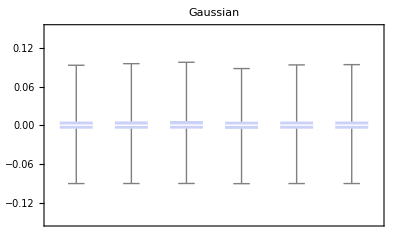
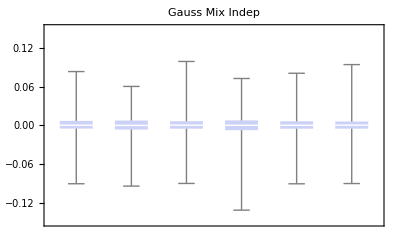
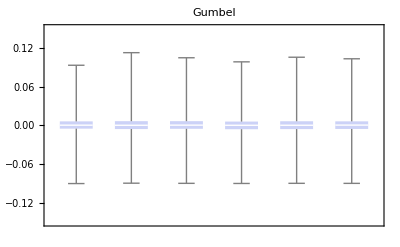
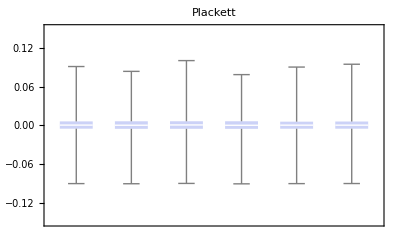
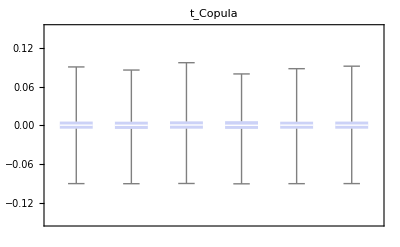
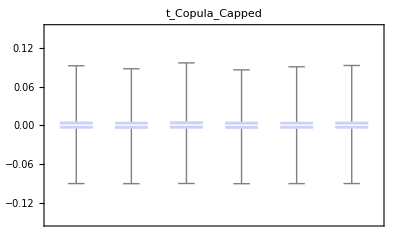

```mathematica
p
```

```mathematica
Export[NotebookDirectory[]<> "../latex/_pics/PL_dynamic_out.pdf", Grid[{{p⟦3⟧,p⟦7⟧,p⟦1⟧,p⟦2⟧},{p⟦5⟧,p⟦6⟧,p⟦9⟧,p⟦4⟧}}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/PL_dynamic_out.pdf

```mathematica
Dimensions[dFull]
```

{9,376,9}

```mathematica
dFull[[2, 1;;10]]
```

(Date | unhedged | future | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-02-03 | 0.0671809 | 0.0363173 | 0.0457928 | 0.0469858 | 0.0514625 | 0.0429908 | 0.0501683 | 0.0492679
2021-02-02 | 0.0522528 | 0.0613977 | 0.0147848 | 0.0168907 | 0.024776 | 0.00983109 | 0.0224992 | 0.0209138
2021-02-01 | -0.0415226 | -0.0263533 | -0.0250686 | -0.0259701 | -0.0293699 | -0.0229586 | -0.0283843 | -0.0276999
2021-01-29 | 0.059664 | 0.0641463 | 0.0207252 | 0.0229154 | 0.0311142 | 0.0155728 | 0.0287471 | 0.0270988
2021-01-28 | 0.0452987 | 0.0337738 | 0.0250055 | 0.0261368 | 0.0303828 | 0.0223486 | 0.0291552 | 0.0283012
2021-01-27 | -0.110154 | -0.0966491 | -0.0492125 | -0.0525257 | -0.0341491 | -0.0396941 | -0.061622 | -0.0587079
2021-01-26 | 0.0683149 | 0.0507328 | 0.0381703 | 0.039881 | 0.030283 | 0.0332074 | 0.0445339 | 0.0430503
2021-01-25 | -0.0323413 | -0.00160643 | -0.0313289 | -0.0313855 | -0.0310692 | -0.0311652 | -0.03154 | -0.0314907
2021-01-22 | -0.0128355 | -0.0492799 | 0.016487 | 0.014869 | 0.0238778 | 0.0211506 | 0.0104409 | 0.0118573)

```mathematica
d=dFull⟦1⟧;
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

```mathematica
extremes=Sort[Abs[d[[2;;,2]]]][[-20;;]];
pos=Flatten[Table[Position[Abs[d[[;;,2]]],extremes[[k]]], {k,1,Length[extremes]}]];
```

```mathematica
pos
```

{66,324,222,34,344,317,18,358,51,7,42,31,193,326,225,134,227,191,20,230}

```mathematica
p1=DateListPlot[{dates,d[[2;;,2]]}ᵀ,PlotRange->{-0.3,0.25},PlotTheme->"Classic",Joined->True,PlotStyle->Thick,AspectRatio->1/4,PlotRange->Full,PlotLabel->"Bitcoin spot"];
```

```mathematica
p1a=DateListPlot[Transpose[{dates⟦pos-1⟧,d[[pos,2]]}],PlotStyle->{Red,Thick},Joined->False];
```

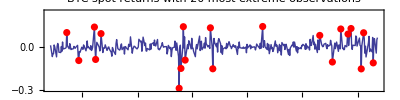

```mathematica
p1b=Show[p1,p1a, PlotLabel->"BTC spot returns with 20 most extreme observations",AspectRatio->1/4]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/BTCspot_with_extremes.pdf", p1b];
```

```mathematica
p2=DateListPlot[{dates,d[[2;;,3]]}ᵀ,PlotRange->{-0.3,0.25},PlotTheme->"Classic",Joined->True,PlotStyle->Thick,AspectRatio->1/4,PlotRange->Full,PlotLabel->"Bitcoin future"];
```

```mathematica
p2a=DateListPlot[Transpose[{dates⟦pos-1⟧,d⟦pos,3⟧}],PlotStyle->{Red,Thick},Joined->False];
```

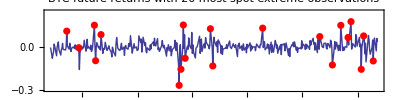

```mathematica
p2b=Show[p2,p2a, PlotLabel->"BTC future returns with 20 most spot extreme observations",AspectRatio->1/4]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/BTCfuture_with_extremes.pdf", p2b];
```

```mathematica
For[kk=1, kk≤Length[copulas], kk++,
d=dFull⟦kk⟧;
p=Table[Show[
DateListPlot[{dates,d⟦2;;All,m⟧}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods⟦m-3⟧,PlotTheme->"Classic",Joined->True,PlotStyle->Thick(*,AspectRatio->1/4*)],
DateListPlot[Transpose[{dates⟦pos-1⟧,d⟦pos,m⟧}],PlotStyle->{Red,Thick},Joined->False]
],
 {m,4,9}];
Export[NotebookDirectory[] <> "../latex/_pics/PL_dyn_series_"<> copulas⟦kk⟧ <> ".pdf",Grid[{{p⟦1⟧,p⟦2⟧,p⟦3⟧},{p⟦4⟧,p⟦5⟧,p⟦6⟧},{"",copulas⟦kk⟧}}]];
]
```

```mathematica
Dimensions[dFull]
```

{9,376,9}